```mathematica
aB=0.5291772085936*10^-10; (*m*)
me=9.10938356*10^-31; (*kg*)
ℏ=1.054571817*10^-34; (*J×s*)
e=1.602176620*10^-19; (*C*)
T=300;(*K*)
kT=T*8.617333262*10^-5;(*eV*)
meffeA=0.6;(*Subscript[m, e]*)
meffeB=0.5;(*Subscript[m, e]*)
meffhA=10;
meffhB=10;
ℏΩLOA=0.04;(*eV*)
ℏΩLOB=0.04;(*eV*)
σdA=9.3;(*eV*)
σdB=9.1;(*eV*)
cLA=3.98*10^3;(*m/s*)
cLB=3.33*10^3;(*m/s*)
ρA=4.42*10^3;(*kg/m^3*)
ρB=7.59*10^3;(*kg/m^3*)
VcellA=858.43;(*Å^3*)
VcellB=801.37;(*Å^3*)
ϵstA=10.4;
ϵstB=10.4;
ϵinfA=3.2;
ϵinfB=3.2;
AtypeConcentration=0.5;
meffe=(AtypeConcentration/meffeA+(1-AtypeConcentration)/meffeB)^-1;
meffh=(AtypeConcentration/meffhA+(1-AtypeConcentration)/meffhB)^-1;
ℏΩLOperϵ=AtypeConcentration*ℏΩLOA*(1/ϵinfA-1/ϵstA)+(1-AtypeConcentration)*ℏΩLOB*(1/ϵinfB-1/ϵstB);
ℏΩLO=AtypeConcentration*ℏΩLOA+(1-AtypeConcentration)*ℏΩLOB;
sqσdpercL=AtypeConcentration*σdA^2/cLA+(1-AtypeConcentration)*σdB^2/cLB;
cL=AtypeConcentration*cLA+(1-AtypeConcentration)*cLB;
ρ=(ρA*AtypeConcentration*VcellA+ρB*(1-AtypeConcentration)*VcellB)/(AtypeConcentration*VcellA+(1-AtypeConcentration)*VcellB);
Vo=AtypeConcentration*VcellA+(1-AtypeConcentration)*VcellB;
```

```mathematica
listmass={{0,0.52},{0.45,0.52},{0.55,1.0},{0.6,2.0},{1.3,3.5},{2.5,3.0},{3,2.2},{3.5,1.8},{6.0,1.6},{9,1.2},{12,1.1},{15,1.0},{20,1.0},{40,1.0},{100,1.0}};
mint=Interpolation[listmass,InterpolationOrder->1,Method->"Spline"];
```

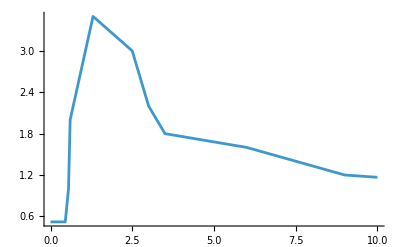

```mathematica
Plot[mint[x],{x,0,10},PlotRange->{Full,{0,All}},ScalingFunctions->{None,None}]
```

```mathematica
n[hΩ_]:=1/(Exp[hΩ/kT]-1);
v[Ε_,m_]:=√((2(Ε*e))/(m*me));
τPLOeminv[Ε_,mpr_]:=√(mpr/me)*(ℏΩLOperϵ*e)/(√2*aB)*1/(√(Ε*e))*(n[ℏΩLO]+1/2+1/2)*Log[Abs[(√Ε+√(Ε-ℏΩLO))/(√Ε-√(Ε-ℏΩLO))]]*If[Ε-ℏΩLO>=0,1,0];
τPLOabsinv[Ε_,mpr_]:=√(mpr/me)*(ℏΩLOperϵ*e)/(√2*aB)*1/(√(Ε*e))*(n[ℏΩLO]+1/2-1/2)*Log[Abs[(√Ε+√(Ε+ℏΩLO))/(√Ε-√(Ε+ℏΩLO))]];
τDLAeminv[Ε_,mpr_]:=(√(mpr*me))/(4*√2*π*ℏ)*(sqσdpercL*e^2)/ρ*1/(√(Ε*e))*Quiet@NIntegrate[(n[(ℏ*q*cL)/e]+1/2+1/2)*q^2(**(1-(ℏ*q)^2/(8mpr m Ε e))*),{q,0,Min[2.0*(√(2*mpr*me*Ε*e)-(√(cL*mpr*me))^2)/ℏ,π/((Vo*10^-30)^(1/3))]}]*If[Ε-(mpr*me*cL^2)/(2e)>=0,1,0];
τDLAabsinv[Ε_,mpr_]:=(√(mpr*me))/(4*√2*π*ℏ)*(sqσdpercL*e^2)/ρ*1/(√(Ε*e))*Quiet@NIntegrate[(n[(ℏ*q*cL)/e]+1/2-1/2)*q^2(**(1-(ℏ*q)^2/(8mpr m Ε e))*),{q,0,Min[2.0*(√(2*mpr*me*Ε*e)+cL*mpr*me)/ℏ,π/((Vo*10^-30)^(1/3))]}];
```

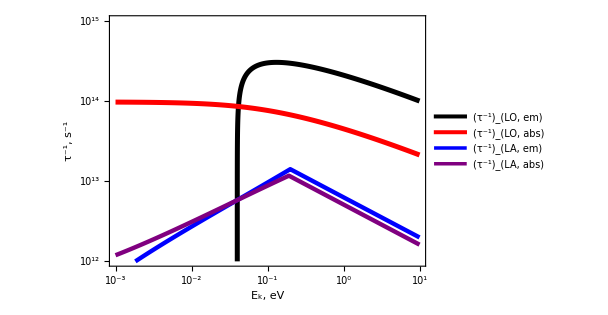

```mathematica
Plot[{τPLOeminv[Ε,meffe],τPLOabsinv[Ε,meffe],τDLAeminv[Ε,meffe],τDLAabsinv[Ε,meffe]},{Ε,0.001,10},PlotRange->{{10^-3,10},{10^12,10^15}},PlotPoints->10^3,Frame->True, FrameStyle->Directive[Thickness[0.002],Black],FrameLabel->{Style["E_k, eV",18,Black,FontFamily->"Times"],Style["τ^-1, s^-1",18,Black,FontFamily->"Times"]},PlotStyle->{{Thickness[0.008],Black},{Thickness[0.008],Red},{Thickness[0.007],Blue},{Thickness[0.007],Purple}},LabelStyle->{Directive[18],Black,FontFamily->"Times"},AspectRatio->0.7,PlotLegends->{"(τ^-1)_(LO, em)"," (τ^-1)_(LO, abs)","(τ^-1)_(LA, em)"," (τ^-1)_(LA, abs)"},ScalingFunctions->{"Log10","Log10"},FrameTicks->{{{{10^11,"10^11"},{10^12,"10^12"},{10^13,"10^13"},{10^14,"10^14"},{10^15,"10^15"}},{{10^11,""},{10^12,""},{10^13,""},{10^14,""},{10^15,""}}},{{{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"},{10^0,"10^0"},{10^1,"10^1"}},{{10^-3,""},{10^-2,""},{10^-1,""},{10^0,""},{10^1,""}}}},ImageSize->450]
```

```mathematica
Export[NotebookDirectory[]<>"PhAIT_PLO_em_e.txt",Table[{Ε,(τPLOeminv[Ε,meffe]+10^9)^-1},{Ε,ℏΩLO,8,0.01}],"Table"]
```

```mathematica
Export[NotebookDirectory[]<>"PhAIT_PLO_abs_e.txt",Table[{Ε,(τPLOabsinv[If[Ε==0,0.0001,Ε],meffe]+10^9)^-1},{Ε,0,8,0.01}],"Table"]
```

```mathematica
Export[NotebookDirectory[]<>"PhAIT_DLA_em_e.txt",Table[{Ε,(τDLAeminv[Ε,meffe]+10^9)^-1},{Ε,0,100,0.01}],"Table"]
```

```mathematica
Export[NotebookDirectory[]<>"PhAIT_DLA_abs_e.txt",Table[{Ε,(τDLAabsinv[If[Ε>=(meffe*me*cL^2)/(2e),Ε,(meffe*me*cL^2)/(2e)],meffe]+10^9)^-1},{Ε,0,100,0.01}],"Table"]
```